A Computational Model for Invasion Sports

Willem nielsen

### It’s All About Space

My idea here is that in any invasion sport, the attackers are trying arrange themselves to maximize the number of different ways they can score. For example, in basketball, a pick and roll creates a dual-threat of the dribbler driving to the basket or passing to the roller for a layup. In soccer you often see one player making a run which frees up another player.

Put more generally, the attackers are trying to maximize the number of dangerous places the ball can be in a given time frame. This means the defenders cannot prevent all the threats.

What’s interesting is if you encode this simple strategy into a computational model, you get realistic play:

The attackers are trying to reach the red endzone without letting the defenders touch the ball. In this case the defense is overaggressive going for a steal. The offense then takes advantage by cutting straight to the endzone with a series of passes. Now, what’s cool about this model is we can scale it up and down and see how things change.

Let’s start with the most basic game and see what happens as we increase the number of players.

2v3 Game:

Here the attackers weren’t able to progress all the way to the endzone, eventually giving up a steal. Again, the attackers are trying to maximize threatening ball positions, so less players means less potential passes. Let’s add an attacker.

3v3 Game:

The attackers were able to leverage the extra player to score a touchdown. Let’s add a defender now.

3v4 Game:

The extra defender led to a steal. So we’re seeing examples of how the model scales, but can we make this more precise? One approach is to simply track the ball, here’s a path of the ball from the previous game:

-Graphics-

Now let’s track the ball over many games. Let’s increase the court length and game length to get a sense for the rate of progression. This time let’s increase the arm strength and see how that affects the attackers’ success.

2v3:

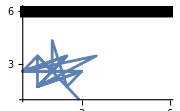
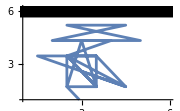
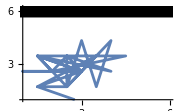
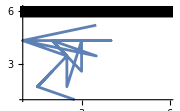
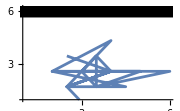
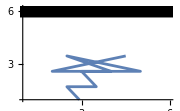
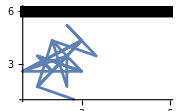
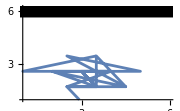

2v3 with higher arm strength:

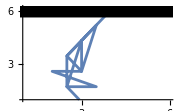
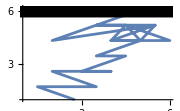
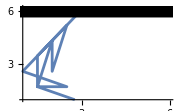
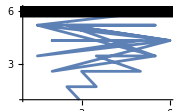
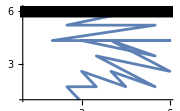
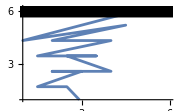
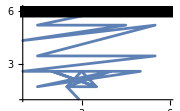
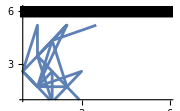

So you can see they are throwing longer passes and progressing further, scoring 9/10 times.

### Squeezing Dimensions

Another surprising discovery was that these scaling laws of arm strength can be captured in 1 dimension. Here we have a passer (black), an attacker (blue) and a defender (red). The ball moves like a knight in chess, “flying above” the players. Based on the position of the defender, the attackers will either go for a short or long pass.

The defender gives ample space forcing the offense to go for a short pass:

The defender gets too close allowing the attacker to run by him for a long pass:

Note that the attacker positions himself right in the place where he can catch a long or short pass. If he lines up too far away, he won’t have the long pass option and the defender can then simply cut off the short pass. If he lines up too close, he won’t maximize the yardage gain.

We can then chain these passes together and add a touch of randomness to get a sense for the progression of the attacking team:

5 consecutive passes

So the attackers made it about a third of the way up the field. Let’s see what happens if we double the arm strength.

They made it about 2/3 of the way this time. One subtlety here is that not only is the attackers rate of progression proportional to arm strength, but also the dispersion of the players. By allowing long passes, you incentivize off-ball attackers to move further away from the ball.

This used to drive me nuts while coaching youth players. Because they aren’t strong or skilled enough to throw long passes, the defense is incentivized to play hyper-aggressively, developing bad habits, and the offense is incentivized to crowd the ball. You address this by creating advantages for the attackers like extra players, or being the point guard yourself.

### Looking Off The Court

For me, It’s been thoroughly enjoyable to distill effects that I’ve observed in practice into the simplest possible computational form. I have much more that I wasn’t quite ready to show here, like an algorithm that works for 10+ players and a much larger court, or a graph for the 1D game that allows you to see the precise optimal positioning for attacker and defender. I’m also excited to look outside the world of sports and model other invasion dynamics like pack hunting and war. My time at the Wolfram Summer School allowed me to build a strong foundation and I feel like this is just the beginning... Thank you for reading.

## Acknowledgments

The Wolfram Summer School was a life-changing experience for me. Thank you to Eric James Parfitt, John McNally, Stephen Wolfram and all the others who made this possible.

## Access the Full Code

Scan or visit wolfr.am/ShortURL.

These are a short URL and a QR code used to condense large blocks of code. They will lead to the Wolfram Community version of your project where the full code can be found. Our publishing team will provide these for you. They can be placed anywhere in your project where we want to condense code for print.

## Cite This Notebook

“A Computational Model for Invasion Sports”
by Willem Nielsen
https://community.wolfram.com/groups/-/m/t/3210765?p_p_auth=mnG1KCWE